# Inverse localization length

```mathematica
M[μ_,x_]=Sqrt[BesselJ[μ,x]^2+BesselY[μ,x]^2];
κ[x_]=-x*D[M[μ,x],x]/M[x]
```

-((x (BesselJ[μ,x] (BesselJ[-1+μ,x]-BesselJ[1+μ,x])+BesselY[μ,x] (BesselY[-1+μ,x]-BesselY[1+μ,x])))/(2 √(BesselJ[μ,x]^2+BesselY[μ,x]^2) M[x]))

```mathematica
μ=0;Limit[-((x (BesselJ[μ,x] (BesselJ[-1+μ,x]-BesselJ[1+μ,x])+BesselY[μ,x] (BesselY[-1+μ,x]-BesselY[1+μ,x])))/(2 (BesselJ[μ,x]^2+BesselY[μ,x]^2))),x->0]
```

0

```mathematica
FullSimplify[-(x (-2 BesselJ[0,x] BesselJ[1,x]-2 BesselY[0,x] BesselY[1,x]))/(2 (BesselJ[0,x]^2+BesselY[0,x]^2))]
```

(x (BesselJ[0,x] BesselJ[1,x]+BesselY[0,x] BesselY[1,x]))/(BesselJ[0,x]^2+BesselY[0,x]^2)

```mathematica
Simplify[%3]
```

1/2

```mathematica
Normal[Series[κ[x],{x,0,1}]]
```

((2^(-2-2 μ) x^(2+4 μ) Cos[π μ] Cos[π (1+μ)] Gamma[-1-μ] Gamma[-μ])/π^2-(2^(-2 μ) x^(4 μ) Cos[π (-1+μ)] Cos[π μ] Gamma[1-μ] Gamma[-μ])/π^2-(2^(-2 μ) x^(4 μ))/(Gamma[μ] Gamma[1+μ])+(2^(2 μ) Gamma[μ] Gamma[1+μ])/π^2)/((2^(-2 μ) x^(4 μ) Cos[π μ]^2 Gamma[-μ]^2)/π^2+(2 x^(2 μ) Cos[π μ] Gamma[-μ] Gamma[μ])/π^2+(2^(2 μ) Gamma[μ]^2)/π^2+(2^(-2 μ) x^(4 μ))/Gamma[1+μ]^2)

```mathematica
FullSimplify[Gamma[5/3]/Gamma[2/3]-(x^(4/3) (Gamma[1/3] Gamma[2/3]-Gamma[-2/3] Gamma[5/3]))/(4 2^(1/3) Gamma[2/3]^2)]
```

2/3-(π x^(4/3))/(2^(1/3) √3 Gamma[2/3]^2)

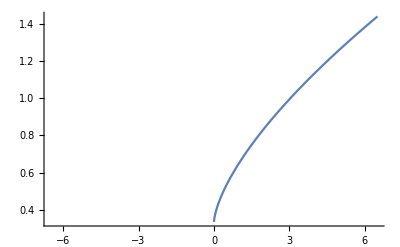

```mathematica
Plot[Gamma[4/3]/Gamma[1/3]-(x^(2/3) (-Gamma[1/3] Gamma[2/3]+Gamma[-1/3] Gamma[4/3]))/(2 2^(2/3) Gamma[1/3]^2),{x,-6.5,6.5}]
```

```mathematica
FullSimplify[%9]
```

((π^2 x^(4 μ) (x^2-8 μ (1+μ)+x^2 Cos[2 π μ]) Csc[π μ]^2)/(2 (1+μ))+4^(1+2 μ) Gamma[μ] Gamma[1+μ]^3)/(4 (π^2 x^(4 μ) Csc[π μ]^2+4^μ Gamma[μ] Gamma[1+μ] (-2 π x^(2 μ) Cot[π μ]+4^μ Gamma[μ] Gamma[1+μ])))

```mathematica
Manipulate[x=Sqrt[y];Plot[{-((√y (BesselJ[μ,√y] (BesselJ[-1+μ,√y]-BesselJ[1+μ,√y])+BesselY[μ,√y] (BesselY[-1+μ,√y]-BesselY[1+μ,√y])))/(2 (BesselJ[μ,√y]^2+BesselY[μ,√y]^2))),μ*x^((1/2-μ))},{y,0,1},PlotRange->{0,1}],{μ,0,1}]
```

```mathematica
μ=ν;D[M[x],x]
```

```mathematica
Normal[Series[(BesselJ[ν,x] (BesselJ[-1+ν,x]-BesselJ[1+ν,x])+BesselY[ν,x] (BesselY[-1+ν,x]-BesselY[1+ν,x]))/(2 √(BesselJ[ν,x]^2+BesselY[ν,x]^2)),{x,0,1}]]
```

(√(x^(-2 ν) ((2^(-2 ν) x^(4 ν) Cos[π ν]^2 Gamma[-ν]^2)/π^2+(2 x^(2 ν) Cos[π ν] Gamma[-ν] Gamma[ν])/π^2+(2^(2 ν) Gamma[ν]^2)/π^2+(2^(-2 ν) x^(4 ν))/Gamma[1+ν]^2)) (-(2^(-2-2 ν) x^(1+4 ν) Cos[π ν] Cos[π (1+ν)] Gamma[-1-ν] Gamma[-ν])/π^2+(2^(-2 ν) x^(-1+4 ν) Cos[π (-1+ν)] Cos[π ν] Gamma[1-ν] Gamma[-ν])/π^2-(2^(2 ν) Gamma[ν] Gamma[1+ν])/(π^2 x)+x^(4 ν) (2^(-2 ν)/(x Gamma[ν] Gamma[1+ν])-(2^(-2-2 ν) x (ν Gamma[ν]+ν^2 Gamma[ν]+Gamma[2+ν]+2 ν Gamma[2+ν]))/(ν (1+ν) Gamma[ν] Gamma[1+ν] Gamma[2+ν]))))/((2^(-2 ν) x^(4 ν) Cos[π ν]^2 Gamma[-ν]^2)/π^2+(2 x^(2 ν) Cos[π ν] Gamma[-ν] Gamma[ν])/π^2+(2^(2 ν) Gamma[ν]^2)/π^2+(2^(-2 ν) x^(4 ν))/Gamma[1+ν]^2)

```mathematica
Simplify[%56]
```

-((√(4^-ν x^(2 ν) Cos[π ν]^2 Gamma[-ν]^2+2 Cos[π ν] Gamma[-ν] Gamma[ν]+4^ν x^(-2 ν) Gamma[ν]^2+(4^-ν π^2 x^(2 ν))/Gamma[1+ν]^2) Gamma[1+ν] (π^2 x^(4 ν) (-4 ν (1+ν)+x^2 (1+2 ν)) Gamma[2+ν]+4^(1+2 ν) ν (1+ν) Gamma[ν]^2 Gamma[1+ν]^2 Gamma[2+ν]+x^(4 ν) ν (1+ν) Gamma[ν] (π^2 x^2-x^2 Cos[π ν]^2 Gamma[-1-ν] Gamma[-ν] Gamma[1+ν] Gamma[2+ν]+4 Cos[π ν]^2 Gamma[1-ν] Gamma[-ν] Gamma[1+ν] Gamma[2+ν])))/(4 π x ν (1+ν) Gamma[ν] (π^2 x^(4 ν)+x^(4 ν) Cos[π ν]^2 Gamma[-ν]^2 Gamma[1+ν]^2+2^(1+2 ν) x^(2 ν) Cos[π ν] Gamma[-ν] Gamma[ν] Gamma[1+ν]^2+16^ν Gamma[ν]^2 Gamma[1+ν]^2) Gamma[2+ν]))

```mathematica
y=Sqrt[x];(BesselJ[μ,y] (BesselJ[-1+μ,y]-BesselJ[1+μ,y])+BesselY[μ,y] (BesselY[-1+μ,y]-BesselY[1+μ,y]))/(2 √(BesselJ[μ,y]^2+BesselY[μ,y]^2))/M[Sqrt[x]]^2
```

```mathematica
μ=2;Normal[Series[(BesselJ[μ,√x] (BesselJ[-1+μ,√x]-BesselJ[1+μ,√x])+BesselY[μ,√x] (BesselY[-1+μ,√x]-BesselY[1+μ,√x]))/(2 (BesselJ[μ,√x]^2+BesselY[μ,√x]^2)^(3/2)),{x,0,2}]]
```

-(π √x)/2+1/4 π x^(3/2)

```mathematica
FullSimplify[%6]
```

$Aborted

```mathematica
μ=1/4;NIntegrate[(BesselJ[μ,√x] (BesselJ[-1+μ,√x]-BesselJ[1+μ,√x])+BesselY[μ,√x] (BesselY[-1+μ,√x]-BesselY[1+μ,√x]))/(2 (BesselJ[μ,√x]^2+BesselY[μ,√x]^2)^(3/2))/x^(3/2),{x,0.0000001,1000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000186188}. NIntegrate obtained -291854. and 121.059 for the integral and error estimates.

-291854.

```mathematica
Manipulate[Plot[(BesselJ[μ,√x] (BesselJ[-1+μ,√x]-BesselJ[1+μ,√x])+BesselY[μ,√x] (BesselY[-1+μ,√x]-BesselY[1+μ,√x]))/(2 (BesselJ[μ,√x]^2+BesselY[μ,√x]^2)^(3/2))/x^(3/2),{x,0,10}],{μ,0,10}]
```

```mathematica
Assuming[μ>4,Limit[(BesselJ[μ,√x] (BesselJ[-1+μ,√x]-BesselJ[1+μ,√x])+BesselY[μ,√x] (BesselY[-1+μ,√x]-BesselY[1+μ,√x]))/(2 (BesselJ[μ,√x]^2+BesselY[μ,√x]^2)^(3/2))/x^(3/2),x->0]]
```

$Aborted

```mathematica
Simplify[%2]
```

-((2^(-1/2+2 μ) π x^(-2+μ) (-1+μ) (1+μ) Gamma[1+μ]^3 √((4^-μ x^-μ (π^2 x^(2 μ) (-1+μ) (2-x+2 μ)+x^(2 μ) (-1+μ) (2-x+2 μ) Cos[π μ]^2 Gamma[-μ]^2 Gamma[1+μ]^2+2^(1+2 μ) x^μ (-2+x+2 μ^2) Cos[π μ] Gamma[-μ] Gamma[μ] Gamma[1+μ]^2+16^μ (1+μ) (-2+x+2 μ) Gamma[μ]^2 Gamma[1+μ]^2))/((-1+μ^2) Gamma[1+μ]^2)) (π^2 x^(2 μ) (-1+μ) (x+2 x μ-4 μ (1+μ)) Gamma[2+μ]+4^μ (1+μ) Gamma[μ]^2 Gamma[1+μ] (-x^(1+μ) (-1+μ) μ Cos[π μ] Gamma[-1-μ]+x^(1+μ) Cos[π μ] Gamma[1-μ]+4^μ (-x (-1+μ) μ Gamma[-1+μ]+(4 (-1+μ) μ+x (-1+2 μ)) Gamma[1+μ])) Gamma[2+μ]+x^μ (-1+μ) Gamma[μ] (-x^(1+μ) μ (1+μ) Cos[π μ]^2 Gamma[-1-μ] Gamma[-μ] Gamma[1+μ] Gamma[2+μ]-x^μ (x+2 x μ-4 μ (1+μ)) Cos[π μ]^2 Gamma[1-μ] Gamma[-μ] Gamma[1+μ] Gamma[2+μ]+x (π^2 x^μ μ (1+μ)-4^μ μ (1+μ) Cos[π μ] Gamma[-1+μ] Gamma[-μ] Gamma[1+μ] Gamma[2+μ]+4^μ Cos[π μ] Gamma[-μ] Gamma[1+μ]^2 Gamma[2+μ]))))/(μ Gamma[μ] (π^2 x^(2 μ) (-1+μ) (2-x+2 μ)+x^(2 μ) (-1+μ) (2-x+2 μ) Cos[π μ]^2 Gamma[-μ]^2 Gamma[1+μ]^2+2^(1+2 μ) x^μ (-2+x+2 μ^2) Cos[π μ] Gamma[-μ] Gamma[μ] Gamma[1+μ]^2+16^μ (1+μ) (-2+x+2 μ) Gamma[μ]^2 Gamma[1+μ]^2)^2 Gamma[2+μ]))

```mathematica
Integrate[1/M[Sqrt[x]]^2,{x,0,∞}]
```

$Aborted

```mathematica
μ=0.4;Plot[1/2 ∫((BesselJ[μ,x] (BesselJ[-1+μ,x]-BesselJ[1+μ,x])+BesselY[μ,x] (BesselY[-1+μ,x]-BesselY[1+μ,x]))/(x^2 (BesselJ[μ,x]^2+BesselY[μ,x]^2)))ⅆx]
```

1/2 ∫((BesselJ[μ,x] (BesselJ[-1+μ,x]-BesselJ[1+μ,x])+BesselY[μ,x] (BesselY[-1+μ,x]-BesselY[1+μ,x]))/(x^2 (BesselJ[μ,x]^2+BesselY[μ,x]^2)))ⅆx

```mathematica
Manipulate[Plot[{1/(BesselJ[μ,Sqrt[x]]^2+BesselY[μ,Sqrt[x]]^2)/24π^2,1},{x,0,10}],{μ,0,3},{σ,1,1}]
```

```mathematica
Normal[Series[Log[(x-X)^2+y^2]/2,{x,0,2},{y,0,2}]]
```

y^2/(2 X^2)+x^2 (-1/(2 X^2)+(3 y^2)/(2 X^4))+x (-1/X+y^2/X^3)+Log[X^2]/2

```mathematica
Integrate[x^μ*Log[x],x]
```

(x^(1+μ) (-1+(1+μ) Log[x]))/(1+μ)^2

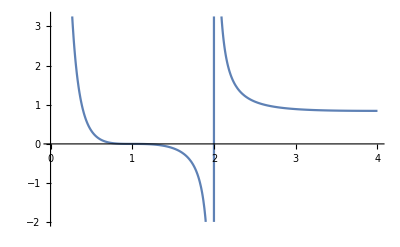

```mathematica
Plot[((x-1)^3/((x-2)*x^2)),{x,0,4}]
```

```mathematica
Normal[(Log[X^2]/2+y^2/(2 X^2)+O[y]^3)+(-1/X+y^2/X^3+O[y]^3) x+O[x]^2]
```

y^2/(2 X^2)+x (-1/X+y^2/X^3)+Log[X^2]/2

```mathematica
Normal[(Log[X^2]/2+y^2/(2 X^2)+O[y]^3)+(-1/X+y^2/X^3+O[y]^3) x+(-1/(2 X^2)+(3 y^2)/(2 X^4)+O[y]^3) x^2+O[x]^3]
```

y^2/(2 X^2)+x^2 (-1/(2 X^2)+(3 y^2)/(2 X^4))+x (-1/X+y^2/X^3)+Log[X^2]/2

```mathematica
BesselJ[1,2]
```

BesselJ[1,2]

```mathematica
M[5,2]
```

√(BesselJ[5,2]^2+BesselY[5,2]^2)

```mathematica
N[√(BesselJ[5,2]^2+BesselY[5,2]^2)]
```

9.93599

```mathematica
N[√(BesselJ[5,2]^2+BesselY[5,2]^2)]
```

9.93599

```mathematica
N[√(BesselJ[2,1]^2+BesselY[2,1]^2)]
```

1.65468